## Project 12 - Javier Salazar 1001144647

1.  Consider a Weibull Distribution, which is widely used for modelling the lifetime of elements. Use Mathematica to evaluate
         μ = Mean[WeibullDistribution[α,β]], σ^2=Variance[WeibullDistribution[α,β]],  density = PDF[WeibullDistribution[α,β],x]
         and  plot on a single graph densities for (α,β) = (2, 1), (2, 4), (3, 6).  
         
         Remark. For  β=1/λ and  α = 1 WeibullDistribution[α,β] turns into exponential distribution ~λ.

. | (2,1) | (2,4) | (3,6)
μ | (√π)/2 | 2 √π | 5.35788
σ^2 | 1-π/4 | 16 (1-π/4) | 3.79198
density | Piecewise[{{2 ⅇ^(-x^2) x, x>0}, {0, True}}] | Piecewise[{{1/8 ⅇ^(-x^2/16) x, x>0}, {0, True}}] | Piecewise[{{1/72 ⅇ^(-x^3/216) x^2, x>0}, {0, True}}]

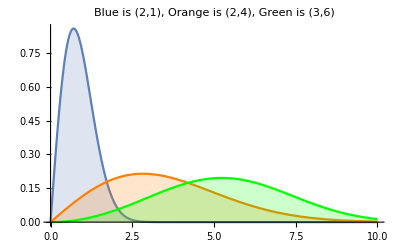

```mathematica
μ1=Mean[WeibullDistribution[2,1]];
μ2=Mean[WeibullDistribution[2,4]];
μ3=Mean[WeibullDistribution[3,6]];
σsquared1=Variance[WeibullDistribution[2,1]];
σsquared2=Variance[WeibullDistribution[2,4]];
σsquared3=Variance[WeibullDistribution[3,6]];
density1=PDF[WeibullDistribution[2,1],x];
density2=PDF[WeibullDistribution[2,4],x];
density3=PDF[WeibullDistribution[3,6],x];
data={{".","(2,1)","(2,4)","(3,6)"},{"μ",μ1,μ2,μ3//N},{"σ^2",σsquared1,σsquared2,σsquared3//N},{"density",density1,density2,density3}};
Grid[data,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}]
g1=Plot[density1,{x,0,10},Filling-> Axis,PlotRange->Full,PlotLabel-> "Blue is (2,1), Orange is (2,4), Green is (3,6)"];
g2=Plot[density2,{x,0,10},Filling-> Axis,PlotStyle->Orange];
g3=Plot[density3,{x,0,10},Filling-> Axis,PlotStyle->Green];
Show[g1,g2,g3]
```

2.  Consider a renewal process N(t) with  X_i ~ WeibullDistribution[2,1] and  m(t) = EN(t)
         (a)  Simulate the sample average m̄(t) = (N^1(t) + ... + N^n(t))/n≈m(t) , for  t ∈{ 0, 0.1,  0.2, .... , 10},  for  n = 100, 1000 
         (b)  Graph m̄(t) together with the linear  asymptote  t/μ+(σ^2- μ^2)/(2 μ^2) (≈ m(t) for large t) , n =100, 1000
         (c) Evaluate the error between  m̄(s)  and  t/μ+(σ^2- μ^2)/(2 μ^2)  for t ∈{0, 1, 2, . . . , 10} ,  n = 1000

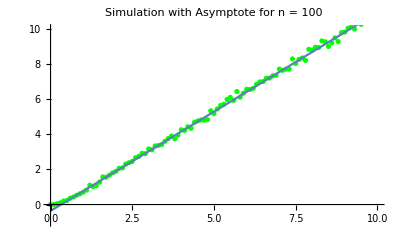

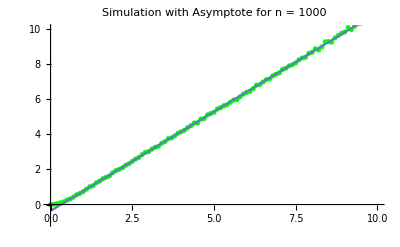

0. | 0.36338
1. | -0.0299989
2. | 0.0366219
3. | -0.0167573
4. | -0.0151364
5. | -0.0365156
6. | -0.0298948
7. | -0.0512739
8. | -0.0156531
9. | 0.0169677
10. | -0.112411

```mathematica
g1=Plot[t/μ +(σsquared1-  μ1^2)/(2 μ1^2),{t,0,10},AxesOrigin->{0,-1}];

n=100;m̄={}; t=10; dt=.1;p=t/dt;
Do[mt={};   
    Do[Numt={};s=0; s=s+RandomVariate[WeibullDistribution[2,1]];
     While[s<i*dt,AppendTo[Numt,s];s=s+RandomVariate[WeibullDistribution[2,1]]];
                  AppendTo[mt,Length[Numt]],
    {n}];
AppendTo[m̄,Mean[mt]],
{i,0,p}]
sampleAverage=Table[{i*.1,m̄[[i+1]]},{i,0,100}]//N;
g2=ListPlot[sampleAverage,PlotRange->{{0,10},{-1,10}},PlotLabel->"Simulation with Asymptote for n = 100",PlotStyle->Green];
Show[g2,g1]

n=1000;m̄={}; t=10; dt=.1;p=t/dt;
Do[mt={};   
    Do[Numt={};s=0; s=s+RandomVariate[WeibullDistribution[2,1]];
     While[s<i*dt,AppendTo[Numt,s];s=s+RandomVariate[WeibullDistribution[2,1]]];
                  AppendTo[mt,Length[Numt]],
    {n}];
AppendTo[m̄,Mean[mt]],
{i,0,p}]
sampleAverage=Table[{i*.1,m̄[[i+1]]},{i,0,100}]//N;
g3=ListPlot[sampleAverage,PlotRange->{{0,10},{-1,10}},PlotLabel->"Simulation with Asymptote for n = 1000",PlotStyle->Green];
Show[g3,g1]

Errors=Table[{i*.1,  m̄[[i+1]]-(i/μ*.1+(σsquared1-  μ1^2)/(2 μ1^2))},{i,0,100,10}]//N;
Grid[Errors,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"]
```

3.   A lifetime of an element has WeibullDistribution[3,6], replacement time is Uniform[0,1] and replacement cost R_i equals 
         twice the replacement time.  Consider a corresponding  Renewal - Reward Process  N(t) with  R(t) = ∑_(i=1)^(N(t)) R_i.
         
          (a)  Simulate n =1000  samples of (R(t))/t for t = 100, 200, 500 and compare to lim_(t→∞) (R(t))/t
          (b)  Graph a typical sample of  R(t)  for t =100

```mathematica
t=100;Rt={};n=1000;
Do[ TotReward=0;s=0;
   r=RandomReal[]+RandomVariate[WeibullDistribution[3,6]];s=s+r;
   While[s<t,TotReward=TotReward+RandomReal[0,2];
              r=RandomReal[]+RandomVariate[WeibullDistribution[3,6]];
              s=s+r];
     AppendTo[Rt,TotReward/t],
{n}];
Mean[Rt]//N
```

{0.,0.}

4.   A specialty store marks down 50% discount on a $20 item, effective immediately whenever the item is not sold for 1 hour
         while reverting  back to the original price immediately after the first discounted item was sold. Suppose that buyers arrive
         according to Poisson process  (renewals are the moments of purchase).  Let “off” corresponds to discounted
         price and “on”  be the regular price periods in the corresponding alternating renewal process, and the day begins with the
         regular price
         
         Consider 100 hours period starting with regular price and assume that buyers arrive with the rate of  λ/per hour.
          
         (a)  Find the long-run proportion of time for the discounted price
         	
       From the hint, the long-run proportion of time for the discounted price, depdendent on λ, is ⅇ^-λ
         	
         (b)  Find the long - run average price to the buyer.  Calculate  long - run average price for  λ = 3, 2, 1, 1/2, 1/3
         (c)  Simulate n =1000 samples to find (off- time in  100hours)/100 and compare to  lim_(t→∞)(off- time in  t hours)/t, λ = 1
         (d)  Graph a typical sample of  on - off  cycles  over 10 hours period ,  λ = 1 (*)
         
         (*) Hint. Renewals  S_n=X_1+ . . . + X_n are buyer arrivals with cycles  X_i = Z_i + Y_i = on + off = min(X_i,1) + [max(X_i,1) - 1].
              Notice that if  X_i≤1 then off part of the cycle is 0.  After simulating a sample  S_1, S_2, . . . S_(N(t)) of renewals on [0, t]
              decompose each  X_i , as above,  to find the on and off parts of the cycle.  Graph on with the value of 20 and off with 10.

```mathematica
n={3,2,1,1/2,1/3};
x={0,0,0,0,0};
For[i=0,i≤ 4,λ=n[[i]];x[[i]]=20(1-ⅇ^-λ) + 10 ⅇ^-λ//N,i++]
data={{"λ ","long-term avg price"},{n[[1]],x[[1]]},{n[[2]],x[[2]]},{n[[3]],x[[3]]},{n[[4]],x[[4]]},{n[[5]],x[[5]]}};
Grid[data,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text",Background->{{Gray,None},{LightGray,None}}]
```

λ  | long-term avg price
3 | 19.5021
2 | 18.6466
1 | 16.3212
1/2 | 13.9347
1/3 | 12.8347

```mathematica
X:=Random[PoissonDistribution[1]]
Z:=Min[X,1];
Y:=Max[X,1]-1;
t=100;n=1000; Ont={};
Do[TotOn=0;
      u=0;on=Z;off=Y;
While[u+on+off<t, u=u+on+off; TotOn=TotOn+on;
         on=Z;off=Y
         ]; 
If[on<t-u, TotOn=TotOn+on,TotOn=TotOn+t-u];AppendTo[Ont,TotOn/t],
{n}];
Mean[Ont]//N;
Print["(off -  time in  100  hours)/100 = ",1-Mean[Ont]//N," and lim_(t → ∞) (off -  time in  t hours)/t = ", 1/ⅇ//N , " with relative absolute error of ",  Abs[1/ⅇ-(1-Mean[Ont])]/(1/ⅇ)*100//N, " %"]
```

(off -  time in  100  hours)/100 = 0.36584 and lim_(t → ∞) (off -  time in  t hours)/t = 0.367879 with relative absolute error of 0.554378 %

```mathematica
X:=Random[PoissonDistribution[1]]
Z:=Min[X,1];
Y:=Max[X,1]-1;
t=10; OnIntervals={};
Do[u=0;on=Z;  off=Y;
    While[u+on+off<t,
               u=u+on+off;AppendTo[OnIntervals,{u-(on+off),u-off}];
               on=Z;off=Y
              ]; 
     If[on<t-u, AppendTo[OnIntervals,{u,u+on}]],AppendTo[OnIntervals,{u,t}]]
```

Do::nliter: Non-list iterator AppendTo[OnIntervals,{u,t}] at position 2 does not evaluate to a real numeric value.

Do[u=0;on=Z;off=Y;While[u+on+off<t,u=u+on+off;AppendTo[OnIntervals,{u-(on+off),u-off}];on=Z;off=Y];If[on<t-u,AppendTo[OnIntervals,{u,u+on}]],AppendTo[OnIntervals,{u,t}]]